## Lesson

Select plot theme:

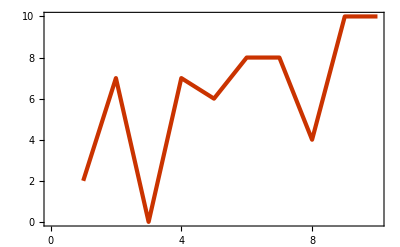

```mathematica
ListLinePlot[RandomInteger[10,10],PlotTheme->"Web"]
```

Fill regions of graph:

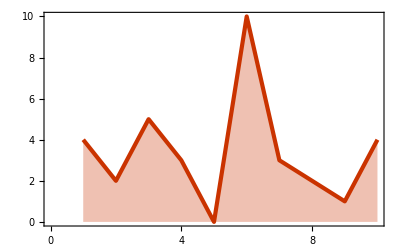

```mathematica
ListLinePlot[RandomInteger[10,10],PlotTheme->"Web",Filling->Axis]
```

Change background colour:

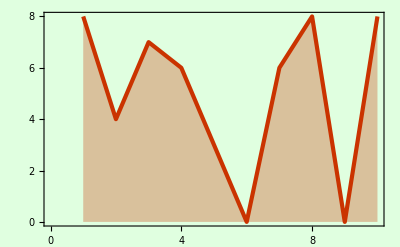

```mathematica
ListLinePlot[RandomInteger[10,10],PlotTheme->"Web",Filling->Axis,Background->LightGreen]
```

Plot certain y values:

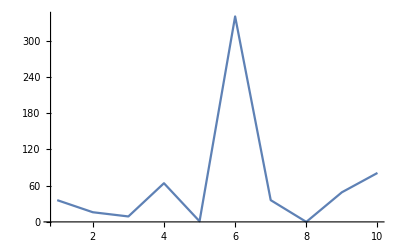

```mathematica
ListLinePlot[{36,16,9,64,1,340,36,0,49,81},PlotRange->All]
```

Plot certain regions:

```mathematica
GeoListPlot[Entity["Country","France"],GeoRange->EntityClass["Country","Europe"]]
```

-Graphics-

Change geoplot style:

```mathematica
GeoListPlot[Entity["Country","France"],GeoRange->EntityClass["Country","Europe"],GeoBackground->"ReliefMap"]
```

-Graphics-

Label data points:

```mathematica
GeoListPlot[{Entity["City",{"LosAngeles","California","UnitedStates"}],Entity["City",{"Chicago","Illinois","UnitedStates"}],Entity["City",{"NewYork","NewYork","UnitedStates"}]},GeoLabels->Automatic]
```

-Graphics-

Join data points:

```mathematica
GeoListPlot[{Entity["City",{"LosAngeles","California","UnitedStates"}],Entity["City",{"Chicago","Illinois","UnitedStates"}],Entity["City",{"NewYork","NewYork","UnitedStates"}]},Joined->True]
```

-Graphics-

Set aspect ratio:

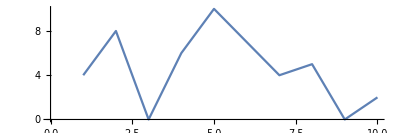

```mathematica
ListLinePlot[RandomInteger[10,10],AspectRatio->1/3]
```

Set image size:

```mathematica
Table[Graphics[Circle[],ImageSize->n],{n,5,50,5}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Set font:

```mathematica
Style["text in a different font",20,FontFamily->"Courier"]
```

text in a different font

Set word orientation:

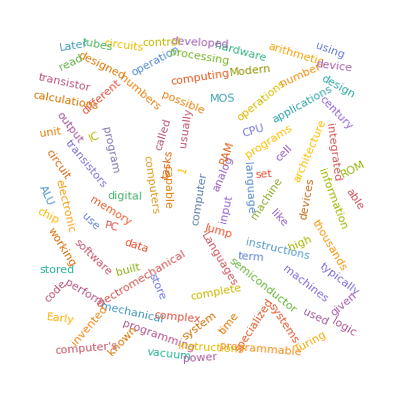

```mathematica
WordCloud[DeleteStopwords[WikipediaData["computer"]],WordOrientation->"Random"]
```

Add frame:

```mathematica
Grid[Table[i j,{i,5},{j,5}],Frame->All]
```

1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10
3 | 6 | 9 | 12 | 15
4 | 8 | 12 | 16 | 20
5 | 10 | 15 | 20 | 25

## Questions

Q1. Create a list plot of Range[10] themed for the web.

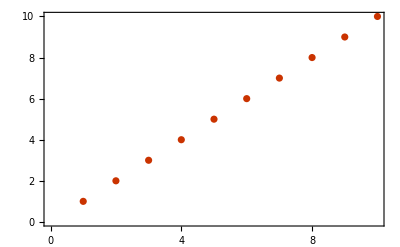

```mathematica
ListPlot[Range[10],PlotTheme->"Web"]
```

Q2. Create a list plot of Range[10] with filling to the axis.

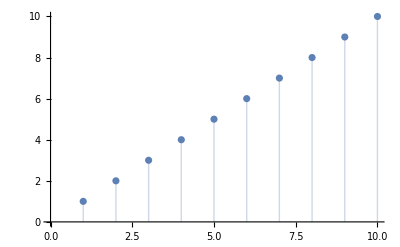

```mathematica
ListPlot[Range[10],Filling->Axis]
```

Q3. Create a list plot of Range[10] with a yellow background.

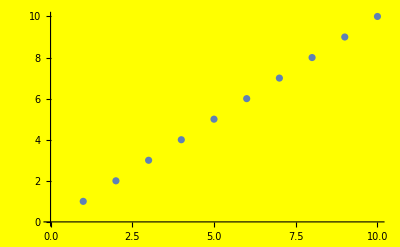

```mathematica
ListPlot[Range[10],Background->Yellow]
```

Q4. Create a map of the world with Australia highlighted.

```mathematica
GeoListPlot[Entity["Country","Australia"],GeoRange->All]
```

-Graphics-

Q5. Create a map of the Indian Ocean with Madagascar highlighted.

```mathematica
GeoListPlot[Entity["Country","Madagascar"],GeoRange->Entity["Ocean","IndianOcean"]]
```

-Graphics-

Q6. Use GeoGraphics to create a map of South America showing topography (relief map).

```mathematica
GeoGraphics[EntityClass["Country","SouthAmerica"],GeoBackground->"ReliefMap"]
```

-Graphics-

Q7. Make a map of Europe with France, Finland and Greece highlighted and labeled.

```mathematica
GeoListPlot[{Entity["Country","France"],Entity["Country","Finland"],Entity["Country","Greece"]},GeoRange->Entity["GeographicRegion","Europe"],PlotLabel->Automatic]
```

-Graphics-

Q8. Make a 12×12 multiplication table as a grid with white type on a black background.

```mathematica
Style[Grid[Table[i j,{i,12},{j,12}],Background->Black],White]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30 | 33 | 36
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60 | 66 | 72
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63 | 70 | 77 | 84
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80 | 88 | 96
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90 | 99 | 108
10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100 | 110 | 120
11 | 22 | 33 | 44 | 55 | 66 | 77 | 88 | 99 | 110 | 121 | 132
12 | 24 | 36 | 48 | 60 | 72 | 84 | 96 | 108 | 120 | 132 | 144

Q9. Make a list of 100 disks with random integer image sizes up to 40.

```mathematica
Table[Graphics[Disk[],ImageSize->RandomInteger[40]],100]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Q10. Make a list of pictures of regular pentagons with image size 30 and aspect ratios from 1 to 10.

```mathematica
Table[Graphics[RegularPolygon[5],ImageSize->30,AspectRatio->RandomReal[{1,10}]],100]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Q11. Make a Manipulate that varies the size of a circle between 5 and 500.

```mathematica
Manipulate[Graphics[Circle[],ImageSize->i],{i,5,500}]
```

Q12. Create a framed 10×10 grid of random colours.

```mathematica
Grid[Table[RandomColor[],10,10],Frame->True]
```

RGBColor[0.7938334171317438, 0.5679483186246779, 0.8234180292407987] | RGBColor[0.2832781298966309, 0.6440410208166363, 0.9261515599345451] | RGBColor[0.35959890743045575, 0.20421029615929287, 0.9287069383854338] | RGBColor[0.4491699173668222, 0.39480817681239655, 0.39455828489307687] | RGBColor[0.600397005456174, 0.4237982788858321, 0.5342780881763418] | RGBColor[0.6160914573165766, 0.5913573864954664, 0.1877536280784844] | RGBColor[0.5950008951393067, 0.17377638323959488, 0.5145999999428221] | RGBColor[0.35486144694613775, 0.8195218453505984, 0.5749883281446899] | RGBColor[0.3945558405749161, 0.35774456274805777, 0.7465814349738102] | RGBColor[0.10577542344425761, 0.05732807694266451, 0.8887401973066413]
RGBColor[0.3731857809407646, 0.6703572101849142, 0.7845933279305966] | RGBColor[0.3771198015359283, 0.9397378427364491, 0.16026257323223092] | RGBColor[0.7022489129050529, 0.8195599935999869, 0.34095900428888326] | RGBColor[0.18693229307800863, 0.896228764788711, 0.2906122599221028] | RGBColor[0.8869459387934768, 0.7622014583710914, 0.386554842079738] | RGBColor[0.40176196540424725, 0.46876484041476796, 0.7531310494810188] | RGBColor[0.9146685812170341, 0.05937624845414158, 0.015212620086846984] | RGBColor[0.045710162486794825, 0.0958072054910939, 0.15460667101373882] | RGBColor[0.07545205035194313, 0.27188603817252055, 0.19575596848242416] | RGBColor[0.8086141863112397, 0.6003404665170227, 0.076155077592299]
RGBColor[0.9358951644255407, 0.9617382805578847, 0.13728585856037712] | RGBColor[0.16510263595323016, 0.2746186467086793, 0.5085986250484298] | RGBColor[0.37994438708481293, 0.6292161033583397, 0.3800246028299852] | RGBColor[0.4250657595682943, 0.8624106949644539, 0.6104156257686655] | RGBColor[0.3892015185211448, 0.8640366206930976, 0.8137266166322863] | RGBColor[0.2715275788153402, 0.03045077128628315, 0.11736149774801863] | RGBColor[0.7774155876453821, 0.40958943420779304, 0.8414912517728979] | RGBColor[0.24442387133691645, 0.05486501296338986, 0.3886819341917085] | RGBColor[0.9920505681183001, 0.024489993662869525, 0.5588991137287782] | RGBColor[0.012139597551890313, 0.9239772226462233, 0.8716744445887521]
RGBColor[0.34948898835762665, 0.5730862345290861, 0.8810598103709535] | RGBColor[0.27685904766133884, 0.2749890254428238, 0.6869598784563617] | RGBColor[0.4324571680864213, 0.185002162108723, 0.4895539757706886] | RGBColor[0.8788713367825163, 0.9428851249663961, 0.5929357878640327] | RGBColor[0.4648045274584094, 0.40423335193463705, 0.8902055596764009] | RGBColor[0.9441670203516805, 0.3500829650693764, 0.04311115389786724] | RGBColor[0.15145235257939782, 0.13902247546486945, 0.8752576801415384] | RGBColor[0.3174802833661108, 0.9239883380349165, 0.39454420011257274] | RGBColor[0.20211469293687223, 0.24863462524916602, 0.8564636969762955] | RGBColor[0.8884719060307986, 0.3408194765321133, 0.887872333301426]
RGBColor[0.8354271776642725, 0.40816825574925564, 0.6516014656205045] | RGBColor[0.20219390515543512, 0.1615283933909728, 0.3174469846244927] | RGBColor[0.7620149158694896, 0.8828292083869447, 0.8988196380798821] | RGBColor[0.4309180312472656, 0.5979588956051971, 0.007662916507411799] | RGBColor[0.9718726736094447, 0.7724687776830756, 0.7931732526197379] | RGBColor[0.4346448903592366, 0.46009182545688354, 0.1820806246732356] | RGBColor[0.7529867927623575, 0.19815572688403238, 0.44245914037195755] | RGBColor[0.2390399100411642, 0.6368235076148121, 0.27809058064623904] | RGBColor[0.42608515594567176, 0.24113104092002824, 0.7752835930089323] | RGBColor[0.7059044113271968, 0.8371334282427665, 0.2671375178924289]
RGBColor[0.5142697524306699, 0.39353484196022803, 0.9858908601081857] | RGBColor[0.6260961056738157, 0.980553707935701, 0.7853687871109174] | RGBColor[0.7139788755949901, 0.7247225457530491, 0.6238092958982839] | RGBColor[0.19845364588241288, 0.3552832255486571, 0.31692652060584847] | RGBColor[0.2815262298851464, 0.8187425263615566, 0.9235905102365451] | RGBColor[0.9828552283298844, 0.49952502647717134, 0.30337183373138066] | RGBColor[0.4368464066479647, 0.5275603668396247, 0.08425485302154345] | RGBColor[0.2146389759386942, 0.0847234513068047, 0.3275627183772769] | RGBColor[0.9630696573956734, 0.008077550465659833, 0.7088470944637635] | RGBColor[0.45247967444606774, 0.34079774314235545, 0.17995846239561142]
RGBColor[0.19676255390651054, 0.7128010358097194, 0.054860803062618535] | RGBColor[0.2285432168199899, 0.22617291104269777, 0.31722981832212405] | RGBColor[0.6772536095861232, 0.2487099197218856, 0.7578030604975134] | RGBColor[0.4414196952388678, 0.2791639593644657, 0.9972401467522909] | RGBColor[0.6797324236422759, 0.3526354885119727, 0.7677888756807079] | RGBColor[0.6073586182108823, 0.82973695206053, 0.6853898017512692] | RGBColor[0.6979906220101582, 0.48420545506776524, 0.454651889859222] | RGBColor[0.13560514874115492, 0.2966775382602176, 0.5922120978323058] | RGBColor[0.6693258980242633, 0.259310262599159, 0.4451953644678128] | RGBColor[0.6037158232468198, 0.6518723383878802, 0.014968972445876583]
RGBColor[0.9035934252717048, 0.36673871559801774, 0.460782996853216] | RGBColor[0.43711105225810964, 0.5402086003470736, 0.7638632245070021] | RGBColor[0.4441469411404997, 0.3324886952482702, 0.7257248966336758] | RGBColor[0.522175212445601, 0.4353010323824098, 0.8273839672987482] | RGBColor[0.6221626005099619, 0.20962348940910314, 0.6350110818541859] | RGBColor[0.2803945620113071, 0.3063996987106934, 0.15492736243434457] | RGBColor[0.6272652205512899, 0.09924906020651592, 0.9798517120562251] | RGBColor[0.5946630807375346, 0.054528935711150694, 0.7776895179919623] | RGBColor[0.7496399468859076, 0.5686396820822679, 0.5554353212655978] | RGBColor[0.2770832385462656, 0.6344358205977363, 0.42414181587591293]
RGBColor[0.6557896687436688, 0.1987899959222148, 0.2983584918367621] | RGBColor[0.03597544341187686, 0.5874142261573039, 0.10089490365111264] | RGBColor[0.9941753371994475, 0.49120298872686585, 0.725074797205439] | RGBColor[0.02531832600945605, 0.13555729988896625, 0.4702607252489457] | RGBColor[0.5332048518109826, 0.7638274799146083, 0.6428333382824676] | RGBColor[0.9509360367633748, 0.6826926823892703, 0.5272755690152429] | RGBColor[0.6112735514703214, 0.6531834243788057, 0.4452926474611443] | RGBColor[0.855596873855625, 0.33009752338263976, 0.9924489413146158] | RGBColor[0.8380460669249232, 0.10889485398630927, 0.9362031683716532] | RGBColor[0.30211255616400146, 0.9435372818288783, 0.17556267484586674]
RGBColor[0.8458786220090713, 0.5646594725107903, 0.8899480370418633] | RGBColor[0.2795195180121337, 0.398537609854158, 0.4390441000287628] | RGBColor[0.5048163983665128, 0.6369269826005242, 0.8161833962941822] | RGBColor[0.7202964939945968, 0.9325223177897921, 0.09140547174744063] | RGBColor[0.3433390197384445, 0.8558147694042164, 0.3901166250574297] | RGBColor[0.528593507450634, 0.30960531079390163, 0.3735253766798674] | RGBColor[0.4108004223004469, 0.8159452209647284, 0.1324911816376919] | RGBColor[0.6962135289317315, 0.9445323184198329, 0.6375787050753987] | RGBColor[0.14470142702174127, 0.7287699386951279, 0.3195907867480887] | RGBColor[0.5419351193826993, 0.46541268298662386, 0.15660662416495952]

Q13. Make a line plot of the lengths of Roman numerals up to 100, with a plot range that would be sufficient for all numerals up to 1000.

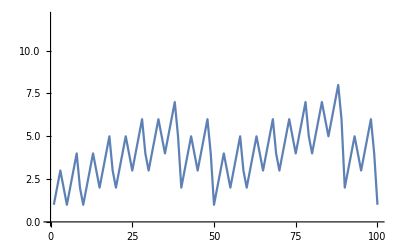

```mathematica
ListLinePlot[StringLength[RomanNumeral[Range[100]]],PlotRange->Max[StringLength[RomanNumeral[Range[1000]]]]]
```

## Extended Questions

+Q1. Create a list plot of Range[10] with a frame included.

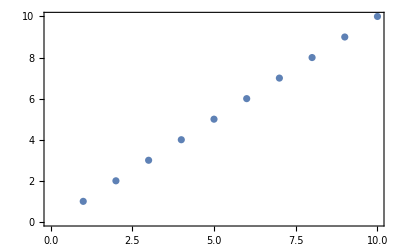

```mathematica
ListPlot[Range[10],Frame->True]
```

+Q2. Create a list plot of Range[10] with a yellow background and a frame.

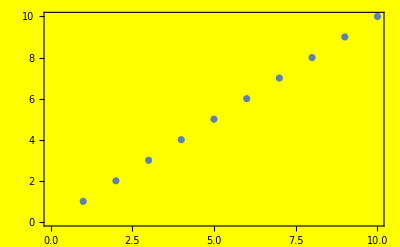

```mathematica
ListPlot[Range[10],Background->Yellow,Frame->True]
```

+Q3. Make a list of list plots of Range[10], with sizes ranging from 50 to 150 in steps of 10.

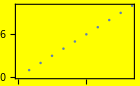
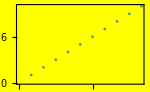
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListPlot[Range[10],Background->Yellow,Frame->True,ImageSize->#]&/@Range[50,150,10]
```

+Q4. Make a line plot of the first 20 squares, filling to the axis.

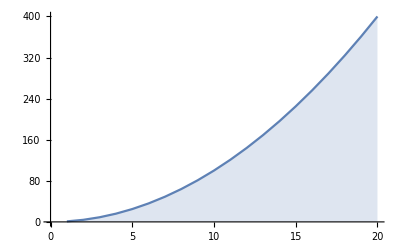

```mathematica
ListLinePlot[Range[20]^2,Filling->Axis]
```

+Q5. Create a relief map of the region around Mount Everest, drawing a disk of radius 100 miles.

```mathematica
GeoGraphics[GeoDisk[Entity["Mountain","MountEverest"],Quantity[100, "Miles"]],GeoBackground->"ReliefMap"]
```

-Graphics-

+Q6. Create a list plot of Range[10] with an aspect ratio of 1.

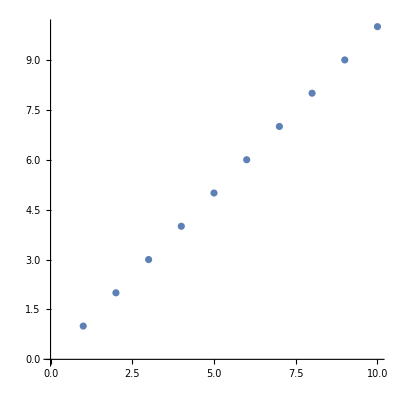

```mathematica
ListPlot[Range[10],AspectRatio->1]
```

+Q7. Make a Manipulate that varies the aspect ratio of a picture of a regular hexagon from 0.1 to 5.

```mathematica
Manipulate[Graphics[RegularPolygon[6],AspectRatio->i],{i,0.1,5}]
```

+Q8. Make a plot of the air temperature in Paris over the past week with the plot range restricted between 50 and 80 degrees.

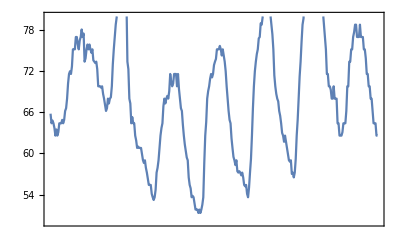

```mathematica
DateListPlot[AirTemperatureData[Entity["City",{"Paris","IleDeFrance","France"}],{DatePlus[Today, -Quantity[1, "Weeks"]],Today}],PlotRange->{50,80}]
```